# Palindromic Number

### Author

Eric W. Weisstein
June 18, 2012

This notebook downloaded from http://mathworld.wolfram.com/notebooks/IntegerSequences/PalindromicNumber.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/PalindromicNumber.html.

For a list of Eric's math packages that may be needed to evaluate this notebook, see Mathematica Information Center's MathSource item 4775.  A list of Eric's utility packages that may be needed to evaluate this notebook may be downloaded from MathSource item 5087.

©2012 Wolfram Research, Inc. except for portions noted otherwise

### Code

```mathematica
<<MathWorld`IntegerSequences`
```

## Enumeration

```mathematica
p=Select[Range[2000],PalindromicQ]
```

{1,2,3,4,5,6,7,8,9,11,22,33,44,55,66,77,88,99,101,111,121,131,141,151,161,171,181,191,202,212,222,232,242,252,262,272,282,292,303,313,323,333,343,353,363,373,383,393,404,414,424,434,444,454,464,474,484,494,505,515,525,535,545,555,565,575,585,595,606,616,626,636,646,656,666,676,686,696,707,717,727,737,747,757,767,777,787,797,808,818,828,838,848,858,868,878,888,898,909,919,929,939,949,959,969,979,989,999,1001,1111,1221,1331,1441,1551,1661,1771,1881,1991}

### Powers of 10

```mathematica
Timing[p=Select[Range[10^5],PalindromicQ];]
```

{0.62091,Null}

```mathematica
Timing[p=Select[Range[10^6],PalindromicQ];]
```

{6.01208,Null}

```mathematica
Timing[p=Select[Range[10^7],PalindromicQ];]
```

{59.69993,Null}

```mathematica
{Timing[p=Select[Range[10^8],PalindromicQ];],MaxMemoryUsed[]/10^9.GB}
```

{{598.98394,Null},3.21881 GB}

```mathematica
{Timing[p=Select[Range[10^9],PalindromicQ];],MaxMemoryUsed[]/10^9.GB}
```

{{6029.42639,Null},32.0206 GB}

```mathematica
Table[Length[Select[p,#<10^n&]],{n,9}]
```

{9,18,108,198,1098,1998,10998,19998,109998}

#### Exact

```mathematica
Table[If[EvenQ[n],2(10^(n/2)-1),11 10^((n-1)/2)-2],{n,9}]
```

{9,18,108,198,1098,1998,10998,19998,109998}

## Not the Sum of Two Palindromes

### Two or Fewer

```mathematica
Take[Complement[Range[Last[p]],
p,
Select[Union[Flatten[Outer[Plus,p,p]]],#≤Last[p]&]],110]
```

{21,32,43,54,65,76,87,98,201,1031,1041,1042,1051,1052,1053,1061,1062,1063,1064,1071,1072,1073,1074,1075,1081,1082,1083,1084,1085,1086,1091,1092,1093,1094,1095,1096,1097,1099,1101,1103,1104,1105,1106,1107,1108,1109,1123,1124,1125,1126,1127,1128,1129,1134,1135,1136,1137,1138,1139,1143,1145,1146,1147,1148,1149,1153,1154,1156,1157,1158,1159,1163,1164,1165,1167,1168,1169,1173,1174,1175,1176,1178,1179,1183,1184,1185,1186,1187,1189,1193,1194,1195,1196,1197,1198,1200,1202,1204,1205,1206,1207,1208,1209,1214,1215,1216,1217,1218,1219,1220}

```mathematica
Take[Complement[Range[Last[p]],
Select[Union[Flatten[Outer[Plus,Prepend[p,0],Prepend[p,0]]]],#≤Last[p]&]],110]
```

{21,32,43,54,65,76,87,98,201,1031,1041,1042,1051,1052,1053,1061,1062,1063,1064,1071,1072,1073,1074,1075,1081,1082,1083,1084,1085,1086,1091,1092,1093,1094,1095,1096,1097,1099,1101,1103,1104,1105,1106,1107,1108,1109,1123,1124,1125,1126,1127,1128,1129,1134,1135,1136,1137,1138,1139,1143,1145,1146,1147,1148,1149,1153,1154,1156,1157,1158,1159,1163,1164,1165,1167,1168,1169,1173,1174,1175,1176,1178,1179,1183,1184,1185,1186,1187,1189,1193,1194,1195,1196,1197,1198,1200,1202,1204,1205,1206,1207,1208,1209,1214,1215,1216,1217,1218,1219,1220}

### Exactly Two

```mathematica
Take[Complement[Range[Last[p]],
Select[Union[Flatten[Outer[Plus,p,p]]],#≤Last[p]&]],110]
```

{1,21,32,43,54,65,76,87,98,111,131,141,151,161,171,181,191,201,1031,1041,1042,1051,1052,1053,1061,1062,1063,1064,1071,1072,1073,1074,1075,1081,1082,1083,1084,1085,1086,1091,1092,1093,1094,1095,1096,1097,1099,1101,1103,1104,1105,1106,1107,1108,1109,1123,1124,1125,1126,1127,1128,1129,1134,1135,1136,1137,1138,1139,1143,1145,1146,1147,1148,1149,1153,1154,1156,1157,1158,1159,1163,1164,1165,1167,1168,1169,1173,1174,1175,1176,1178,1179,1183,1184,1185,1186,1187,1189,1193,1194,1195,1196,1197,1198,1200,1202,1204,1205,1206,1207}

## Plot

#### V5

```mathematica
<<Utilities`Plot`
```

```mathematica
MakeBoxes[ylabel,TraditionalForm]:=RowBox[{"|",RowBox[{"{",RowBox[{"k","≤",RowBox[{"n",":",RowBox[{"k"," ","is"," ","palindromic"}]}]}],"}"}],"|"}]
```

```mathematica
plot1=IntegerListPlot[Take[p,40],PlotStyle->Red,PlotJoined->True,
AxesLabel->TraditionalForm/@{n,ylabel}]
```

⁃Graphics⁃

```mathematica
plot2=ListPlot[MapIndexed[{#1,#2[[1]]}&,Take[p,118]],PlotStyle->Red,PlotJoined->True,
AxesLabel->TraditionalForm/@{n,ylabel}]
```

⁃Graphics⁃

```mathematica
Show[GraphicsArray[{plot1,plot2}],ImageSize->500]
```

⁃GraphicsArray⁃

#### V6

```mathematica
<<Utilities`Plot`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

In V9, RawBoxes has a StripOnInput option which you could use.

  Graphics[{}, Axes -> True, 
   AxesLabel -> RawBoxes[RowBox[{"2", "+"}], StripOnInput -> False]]

That's really the right way, but since this is W|A and thus presumably stuck with V8, that won't help you for now. Dynamic + RawBoxes is heavier weight, but should do what you want.

  Graphics[{}, Axes -> True, 
   AxesLabel -> Dynamic[RawBoxes[RowBox[{"2", "+"}]]]]

```mathematica
MakeBoxes[ylabel,TraditionalForm]:=RowBox[{"|",RowBox[{"{",RowBox[{"k","≤",RowBox[{"n",":",RowBox[{"k"," ","is"," ","palindromic"}]}]}],"}"}],"|"}]
```

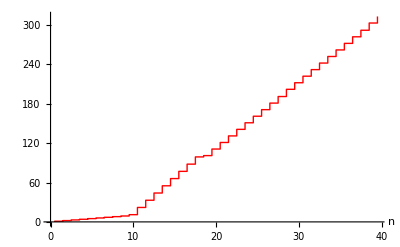

```mathematica
plot1=IntegerListPlot[Take[p,40],PlotStyle->Red,PlotJoined->True,
AxesLabel->{n,Dynamic@RawBoxes@RowBox[{"|",RowBox[{"{",RowBox[{"k","≤",RowBox[{"n",":",RowBox[{"k"," ","is"," ","palindromic"}]}]}],"}"}],"|"}]}]
```

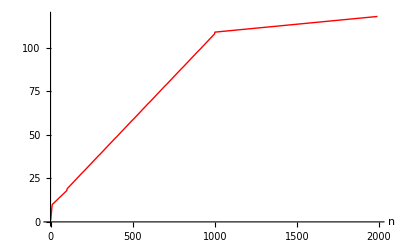

```mathematica
plot2=ListPlot[MapIndexed[{#1,#2[[1]]}&,Take[p,118]],PlotStyle->Red,Joined->True,
AxesLabel->{n,Dynamic@RawBoxes@RowBox[{"|",RowBox[{"{",RowBox[{"k","≤",RowBox[{"n",":",RowBox[{"k"," ","is"," ","palindromic"}]}]}],"}"}],"|"}]}]
```

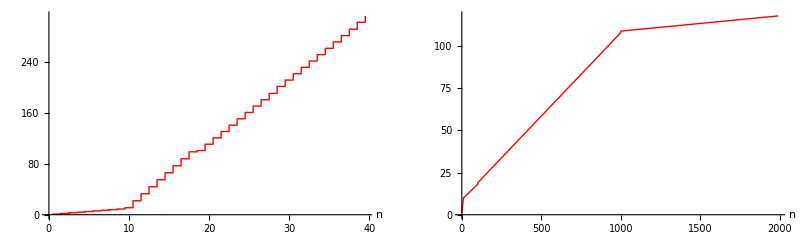

```mathematica
GraphicsRow[{plot1,plot2}]
```

## Sum of Reciprocals

```mathematica
{Length[p],Last[p]}
```

{19998,99999999}

```mathematica
Total[1`30/p]
```

3.37000183240361695347156263236

```mathematica
SequenceLimit[FoldList[Plus,0,1`50/p]]
```

3.370182

```mathematica
SequenceLimit[FoldList[Plus,0,1`100/p]]
```

3.37041322532657135241508115192

```mathematica
SequenceLimit[FoldList[Plus,0,1`200/p]]
```

3.37018022052729364222070689845572570785121433503538

```mathematica
SequenceLimit[FoldList[Plus,0,1`300/p]]
```

3.37

## Palindromic Squares

```mathematica
(l=Length[IntegerDigits[#]]&/@Select[Table[n^2,{n,10^6}],PalindromicQ])//Timing
```

{643.983 Second,{1,1,1,3,3,3,5,5,5,5,5,5,5,6,7,7,7,7,7,9,9,9,9,9,9,9,9,9,9,9,11,11,11,11,11,12}}

```mathematica
Complement[Range[Max[l]],l]
```

{2,4,8,10}

## OEIS

```mathematica
<<Utilities`EISFormat`
```

EISFormat.m version 1.06 by Olivier Gerard and Eric W. Weisstein

e-mail FormatSequence to njas@research.att.com

e-mail LookupFormat   to sequences@research.att.com

or superseeker@research.att.com (single line only)

```mathematica
FormatSequence[{9,18,108,198,1098,1998,10998},
050250,1,
Name->"a(n) is the number of palindromic numbers less than 10^n"]
```

FormatSequence::GiveMeMore: if you can, give enough terms for three lines.

FormatSequence::HeyYou: My respects to you, Master "Eric".

%I A050250 
%S A050250 9,18,108,198,1098,1998,10998
%N A050250 a(n) is the number of palindromic numbers less than 10^n
%A A050250 E. W. Weisstein (eric(AT)weisstein.com), Feb 26, 2004
%O A050250 1,1
%K A050250 nonn,more,new